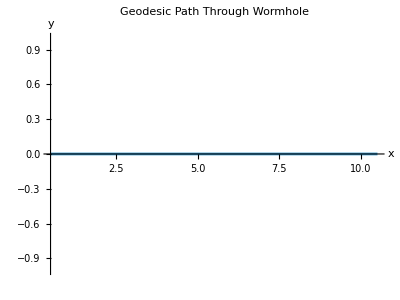

Final position after s = 10: {{10.5,0.}}

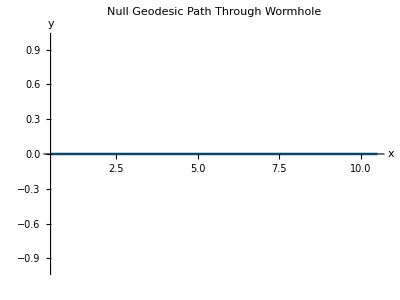

-Graphics3D-

```mathematica
(* ::Title::*)(*Geodesic Traversal and Traversability Check in a 2+1D Wormhole Metric*)(* ::Section::*)(*Define Parameters and Potential*)R0=1.0;
A=1.0;
w=10.0;
ε=0.01;

ΦSafe[x_,y_]:=Module[{r},r=Max[Sqrt[x^2+y^2],ε];
Max[A*(1-R0/r)*Exp[-((r-R0)^2/w^2)],10^-15]];

(* ::Section::*)
(*Define the Metric Components*)

f[x_,y_]:=Exp[2 ΦSafe[x,y]];
invf[x_,y_]:=Exp[-2 ΦSafe[x,y]];

(* ::Section::*)
(*Define the Lagrangian for Geodesic Motion*)

Clear[t,x,y,s]
L=-f[x[s],y[s]] t'[s]^2+invf[x[s],y[s]] (x'[s]^2+y'[s]^2);

(* ::Section::*)
(*Compute Euler-Lagrange Equations*)

eqt=D[D[L,t'[s]],s]-D[L,t[s]]==0;
eqx=D[D[L,x'[s]],s]-D[L,x[s]]==0;
eqy=D[D[L,y'[s]],s]-D[L,y[s]]==0;

(* ::Section::*)
(*Initial Conditions and Numerical Integration for Timelike Geodesic*)

initials={t[0]==0,x[0]==0.5,y[0]==0,t'[0]==1,x'[0]==1,y'[0]==0};
sol=NDSolve[{eqt,eqx,eqy}~Join~initials,{t,x,y},{s,0,10}];

(* ::Section::*)
(*Plot the Geodesic Path*)

ParametricPlot[Evaluate[{x[s],y[s]}/. sol],{s,0,10},PlotRange->All,AxesLabel->{"x","y"},PlotLabel->"Geodesic Path Through Wormhole"]

(* ::Section::*)
(*Output Final Position*)

Print["Final position after s = 10: ",{x[10],y[10]}/. sol]

(* ::Section::*)
(*Null Geodesic Case*)
Lnull=-f[x[s],y[s]] t'[s]^2+invf[x[s],y[s]] (x'[s]^2+y'[s]^2);
eqtN=D[D[Lnull,t'[s]],s]-D[Lnull,t[s]]==0;
eqxN=D[D[Lnull,x'[s]],s]-D[Lnull,x[s]]==0;
eqyN=D[D[Lnull,y'[s]],s]-D[Lnull,y[s]]==0;
nullIC={t[0]==0,x[0]==0.5,y[0]==0,t'[0]==1,x'[0]==1,y'[0]==0};
solNull=NDSolve[{eqtN,eqxN,eqyN}~Join~nullIC,{t,x,y},{s,0,10}];

ParametricPlot[Evaluate[{x[s],y[s]}/. solNull],{s,0,10},PlotRange->All,AxesLabel->{"x","y"},PlotLabel->"Null Geodesic Path Through Wormhole"]

(* ::Section::*)
(*Animated Traversal*)
frames=Table[Graphics[{Red,PointSize[Large],Point[Evaluate[{x[s],y[s]}/. sol]]},PlotRange->{{-1,12},{-2,2}},Axes->True],{s,0,10,0.5}];
ListAnimate[frames]

(* ::Section::*)
(*Potential Visualization*)
Plot3D[ΦSafe[x,y],{x,-2,2},{y,-2,2},PlotLabel->"Potential Φ(x,y)",AxesLabel->{"x","y","Φ"}]
```